## Green function for shear metric perturbation in AdS_5 Vaidya

#### Order in future time upto which the Green function is evaluated

```mathematica
i=200;
```

### Input parameters and assumptions

t = -t_1, and t_1< 0 is the past time, used in the text.

```mathematica
t=15.0;
k=10.0;
```

```mathematica
$Assumptions=And[z∈Reals,z≥0,z≤1,ω∈Reals];
```

### Series expansion of the coefficient of z^(Δ_+)of the v < 0 solution,

lstJ lists the (J̃)_n

```mathematica
lstJ=CoefficientList[Series[(k Sqrt[t^2+2 t z])^(-5/2) BesselJ[-5/2,k Sqrt[t^2+2 t z]],{z,0,1}],z];
Do[AppendTo[lstJ,-((2 (l-1) (l+2-1/2) lstJ[[l]]+k^2 t lstJ[[l-1]])/(t l (l-1)))],{l,2,i}];
```

### Series expansion of the coefficient of z^(Δ_+)of the v > 0 solution,

a[ l ] are arrays which list a_n^j

```mathematica
a[j_]:={};
a[0]={1};
a[1]={0,-I};
a[2]={k^2/12,0,(-7 I a[1][[2]])/12};
a[3]={0,(k^2 a[1][[2]]-9 I a[2][[1]])/21,0,(-9 I a[2][[3]])/21};
For[l=4,l≤i,l++,AppendTo[a[l],(k^2 a[l-2][[1]]+l^2 a[l-4][[1]])/(l (l+4))];
For[j=2,j≤l-3,j++,AppendTo[a[l],(-I (2 l+3) a[l-1][[j-1]]+k^2 a[l-2][[j]]+l^2 a[l-4][[j]])/(l (l+4))]];
For[j=l-2,j≤l-1,j++,AppendTo[a[l],(-I (2 l+3) a[l-1][[j-1]]+k^2 a[l-2][[j]])/(l (l+4))]];
For[j=l,j≤l+1,j++,AppendTo[a[l],(-I (2 l+3) a[l-1][[j-1]])/(l (l+4))]]];
```

### Moments, M, are calculated using eq. (2.14) and (2.15)

```mathematica
M=ConstantArray[lstJ[[1]],1];
For[j=2,j≤i+1,j++,AppendTo[M,1/a[j-1][[j]] (lstJ[[j]]-Sum[M[[l]] a[j-1][[l]],{l,1,j-1}])]];
```

### The thermalizing Green function of eq. (2.18) is constructed and Pade Approximation is used

```mathematica
G[x_]=-4 2^(-3/2) Sqrt[π] k^5 PadeApproximant[Sum[(-I x)^l/l! M[[l+1]],{l,0,i}],{x,0,{i/2-1,i/2+1}}];
```

### Vacuum Green function

```mathematica
Gvac[x_]=-4 2^(-3/2) Sqrt[π] (k/(x+t))^(5/2) BesselJ[-5/2,k (x+t)];
```

### Plot of figure 5

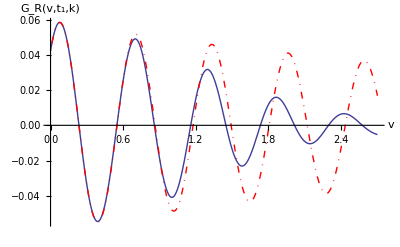

```mathematica
Plot[{G[x],Gvac[x]},{x,0,2.7},PlotRange->Full,PlotStyle->{Thick,{Thick,DotDashed,Red}},AxesLabel->{Style["v",FontSize->16],Style["\!\(\*SubscriptBox[\(G\),\(R\)]\)(v,\!\(\*SubscriptBox[\(t\),\(1\)]\),k)",FontSize->16]}]
```

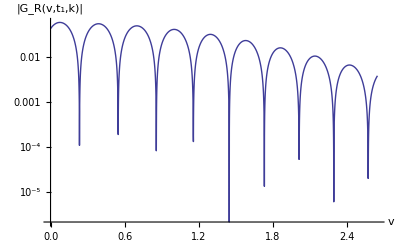

```mathematica
LogPlot[{Abs[G[x]]},{x,0,2.65},PlotRange->Full,PlotStyle->Thick,AxesLabel->{Style["v",FontSize->16],Style["|\!\(\*SubscriptBox[\(G\),\(R\)]\)(v,\!\(\*SubscriptBox[\(t\),\(1\)]\),k)|",FontSize->16]}]
```